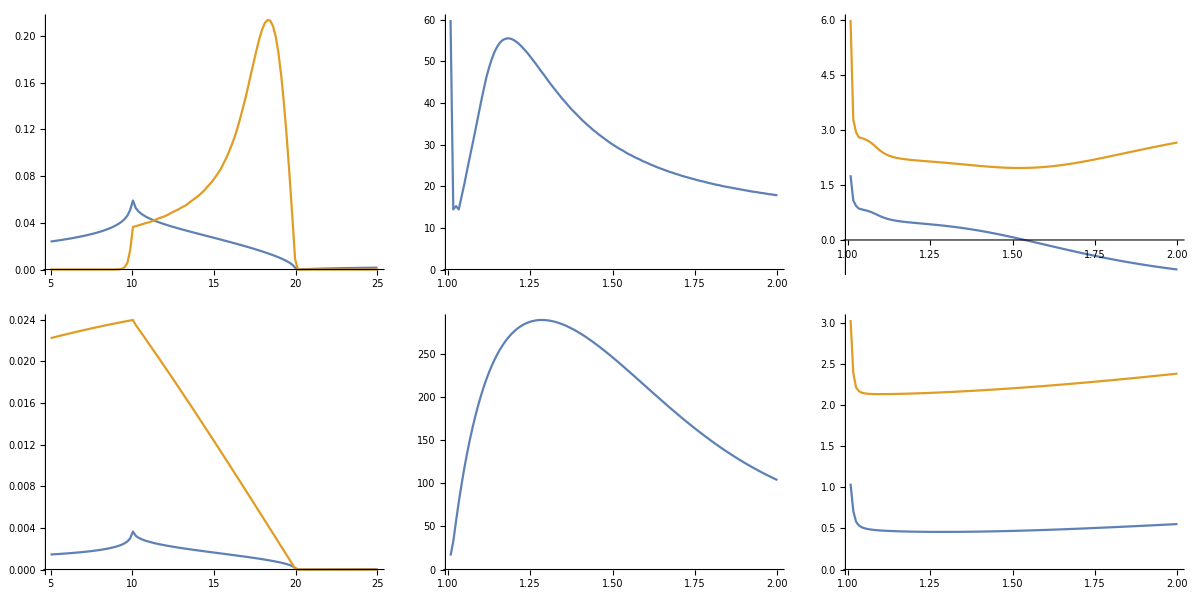
```mathematica
plots=-Graphics-[[1,1]];
```

```mathematica
alphas={1.05,1.1,1.2,1.4,1.6,1.8,2.0};
netquantiles={{0.02,24.27},{2.72,185.97},{5.47,112.25},{12.,49.51},{15.26,31.82},{16.75,24.23},{18.,18.3}};
netmeans={6.957701194790284,65.94724839266505,47.091673291832294,29.09750375,22.799523250000004,20.05474825,18.15126};
MCmeans=First@*Last/@BinaryDeserialize@ByteArray[…];
netV=BinaryDeserialize@ByteArray[…];
netSwitchSkews={0.42950636151244126,0.17921149248284252};
```

```mathematica
ClearAll[Figure];Options[Figure]={ImageSize->400,Gap->1/5};Figure[xlabels_,ylabels_,opt:OptionsPattern[]]:=Figure[#,xlabels,ylabels,opt]&;Figure[subfigs_,xlabels_,ylabels_,OptionsPattern[]]:=GraphicsRow[MapIndexed[Show[#1/.Line[x_]:>{Thickness[.01],Line[x]},Frame->True,PlotStyle->{Thickness[1]},FrameTicksStyle->Directive[Black,16],FrameLabel->Map[Function[x,Style[x,20,Black]],{{ylabels[[First@#2]],""},{xlabels[[First@#2]],Pane["("<>Alphabet[][[First@#2]]<>")",Alignment->Left,ImageSize->OptionValue[ImageSize]]}},{2}],ImageSize->OptionValue[ImageSize](1+OptionValue[Gap])]&]@subfigs,Spacings->-OptionValue[ImageSize]*OptionValue[Gap],ImageSize->OptionValue[ImageSize]*Length[subfigs]];
```

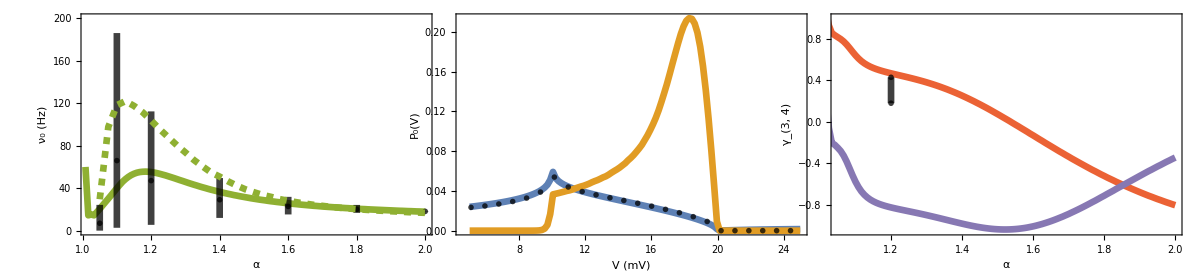

```mathematica
{ListLinePlot[#2,PlotRange->{{1.015,2},{0,200}},PlotStyle->ColorData[97,"ColorList"][[3]]]~Show~ListLinePlot[MapIndexed[{alphas[[First@#2]],#1}&,netquantiles,{2}],PlotStyle->Opacity[.75,Black],PlotRange->All]~Show~ListPlot[Transpose@{alphas,netmeans},PlotStyle->Opacity[.75,Black],PlotMarkers->{"Δ",14}]~Show~ListLinePlot[Transpose@{Range[105/100,2,5/200],MCmeans},PlotStyle->{Dashed,ColorData[97,"ColorList"][[3]]}],
ListLinePlot[#1,PlotRange->All]~Show~ListPlot[netV[[;;;;5]],PlotStyle->Opacity[.75,Black],PlotMarkers->{"Δ",14}],
ListLinePlot[MapAt[Map[{First@#,Last@#-3}&],#3,2],PlotRange->{{1.05,2},{-1.05,1}},PlotStyle->ColorData[97,"ColorList"]~RotateLeft~3]~Show~ListLinePlot[{1.2,#}&/@netSwitchSkews,PlotStyle->Opacity[.75,Black],PlotRange->All,PlotMarkers->{"∇",14}]
}&@@
(Cases[#,Line[data_]:>data,∞]&/@plots)//Figure[{"α","V (mV)","α"},{"ν_0 (Hz)","P_0(V)","γ_(3, 4)"}]
```

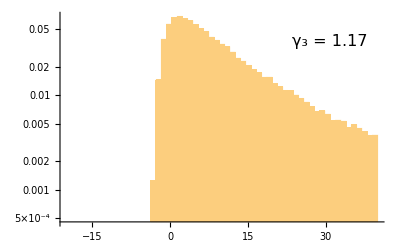
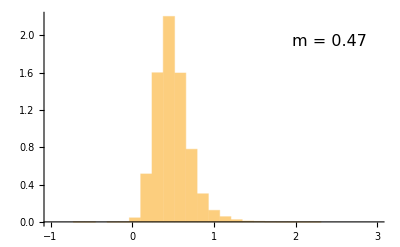
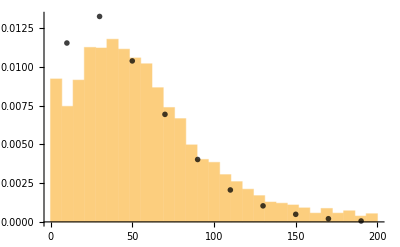
```mathematica
{-Graphics-,-Graphics-,-Graphics-}//Figure[{"Distance from V_r (mV)","γ_3","Firing rate (Hz)"},ConstantArray["Proportion",3],Gap->1/6]
```

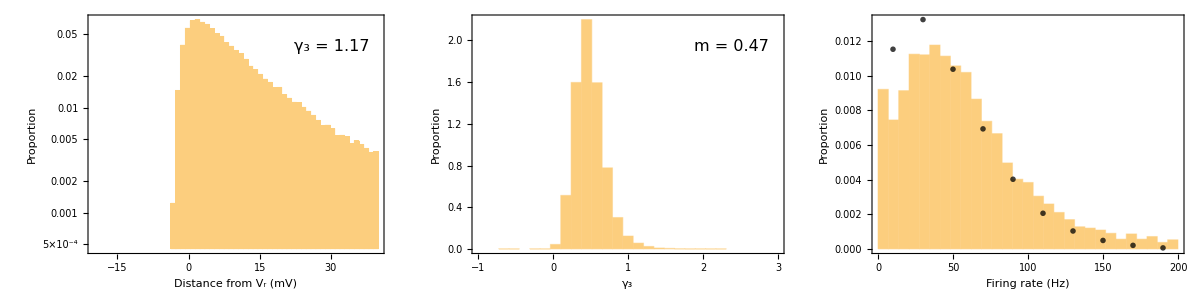

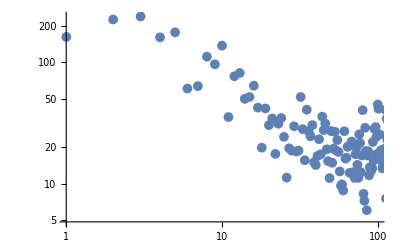
```mathematica
Show[#/.Line[x_]:>{Thickness[.01],Line[x]},Frame->True,PlotStyle->{Thickness[1]},FrameTicksStyle->Directive[Black,16],FrameLabel->Map[Style[#,20,Black]&,{{"",""},{"ω_LFP (Hz)",""}},{2}]]&@-Graphics-
```

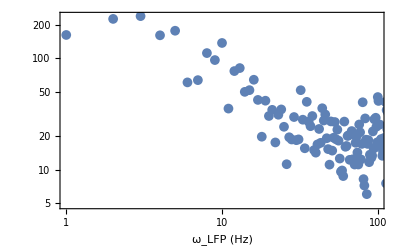

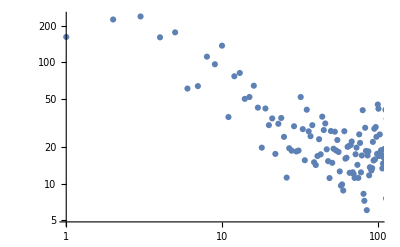
```mathematica
Show[#/.Line[x_]:>{Thickness[.01],Line[x]},Frame->True,PlotStyle->{Thickness[1]},FrameTicksStyle->Directive[Black,16],FrameLabel->Map[Style[#,24,Black]&,{{"",""},{"ω_LFP (Hz)",""}},{2}]]&@Show[-Graphics-,ListLinePlot[Log@{{1,1000},{100,10}},PlotStyle->ColorData[97,"ColorList"]~RotateLeft~4]]
```

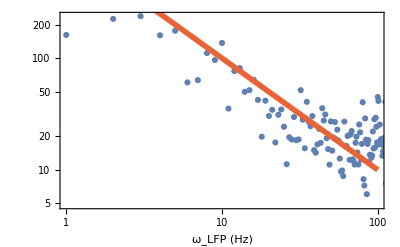

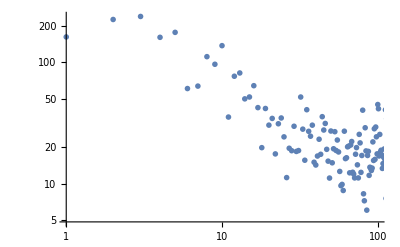
```mathematica
Show[#/.Line[x_]:>{Thickness[.01],Line[x]},Frame->True,PlotStyle->{Thickness[1]},FrameTicksStyle->Directive[Black,16],FrameLabel->Map[Style[#,24,Black]&,{{"",""},{"ω_LFP (Hz)",""}},{2}]]&@Show[-Graphics-,ListLinePlot[Log@{{1,1000},{100,10}},PlotStyle->ColorData[97,"ColorList"]~RotateLeft~4]]
```

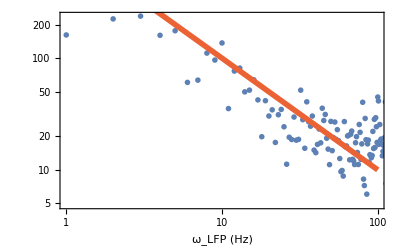

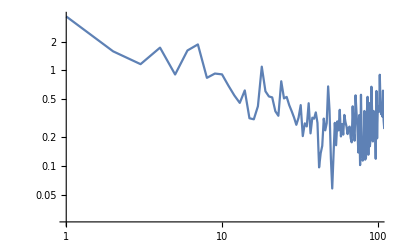
```mathematica
-Graphics-/.Line->Point
```